# Q7

(a)

```mathematica
q7a=DSolve[{y'[t]==t*ⅇ^(3t)-2y[t]},y,t]
```

```mathematica
{{y->Function[{t},ⅇ^(3 t) (-1/25+t/5)+ⅇ^(-2 t) C[1]]}}
Plot[Evaluate[y[t]/.q7a],{t,0,1}]
```

{{y→Function[{t},ⅇ^(3 t) (-1/25+t/5)+ⅇ^(-2 t) C[1]]}}

ReplaceAll::reps: {q7a} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

(b)

```mathematica
qq=NDSolve[{y'[t]==1-(t-y[t])^2,y[2]==1},y,{t,2,3}]
```

NDSolve::ndsz: At t == 3., step size is effectively zero; singularity or stiff system suspected.

{{y→InterpolatingFunction[…]}}

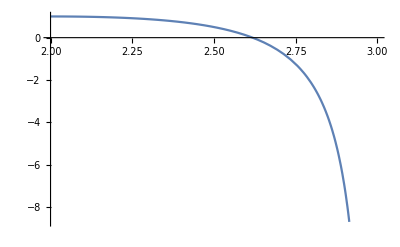

```mathematica
Plot[Evaluate[y[t]/.qq],{t,2,3}]
```

(c)

```mathematica
q7c=NDSolve[{y'[t]==1+y[t]/t,y[1]==2},y,{t,1,2}]
```

{{y→InterpolatingFunction[…]}}

InterpolatingFunction::dmval: Input value {2.00002} lies outside the range of data in the interpolating function. Extrapolation will be used.

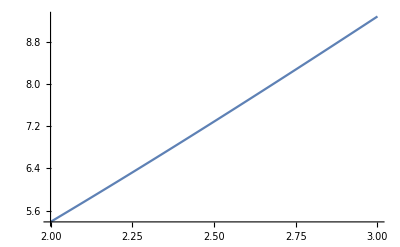

```mathematica
Plot[Evaluate[y[t]/.q7c],{t,2,3}]
```

(d)

```mathematica
q7d=DSolve[{y'[t]==Cos[2*t]+Sin[2*t]},y,t]
```

{{y→Function[{t},C[1]-1/2 Cos[2 t]+1/2 Sin[2 t]]}}

```mathematica
Plot[Evaluate[y[t]/.q7d],{t,0,1}]
```

-Graphics-